```mathematica
w[s_]=1/s^2
K[s_,x_]=s(1+w[s])^((q[x]+1)/2)
```

1/s^2

(1+1/s^2)^(1/2 (1+q[x])) s

```mathematica
Simplify[D[K[s,x],s]]
Simplify[D[K[s,x],x]]
Simplify[D[K[s,x],s,s]]
Simplify[D[K[s,x],s,s]-w[s]/s (1+w[s])^((q[x]-3)/2) (w[s] q[x]+1) (q[x]+1)]
Simplify[D[K[s,x],s,x]/(1+w[s])^((q[x]-1)/2)]
Simplify[D[K[s,x],s,x]/(1+w[s])^((q[x]-1)/2)-1/2 q'[x] ((1-q[x] w[s]) Log[1+w[s]]-2 w[s])]
Simplify[D[K[s,x],x,x]/(1+w[s])^((q[x]+1)/2)]
```

((1+1/s^2)^(1/2 (1+q[x])) (s^2-q[x]))/(1+s^2)

1/2 (1+1/s^2)^(1/2 (1+q[x])) s Log[1+1/s^2] q'[x]

((1+1/s^2)^(1/2 (1+q[x])) (1+q[x]) (s^2+q[x]))/(s (1+s^2)^2)

0

((-2+s^2 Log[1+1/s^2]-Log[1+1/s^2] q[x]) q'[x])/(2 s^2)

0

1/4 s Log[1+1/s^2] (Log[1+1/s^2] q'[x]^2+2 q''[x])

```mathematica
det[s_,x_]=D[K[s,x],s,s] D[K[s,x],x,x] -D[K[s,x],s,x]^2
```

-(-((1+1/s^2)^(-1+1/2 (1+q[x])) q'[x])/s^2+1/2 (1+1/s^2)^(1/2 (1+q[x])) Log[1+1/s^2] q'[x]-((1+1/s^2)^(-1+1/2 (1+q[x])) Log[1+1/s^2] (1+q[x]) q'[x])/(2 s^2))^2+(((1+1/s^2)^(-1+1/2 (1+q[x])) (1+q[x]))/s^3+(2 (1+1/s^2)^(-2+1/2 (1+q[x])) (1+q[x]) (-1+1/2 (1+q[x])))/s^5) (1/4 (1+1/s^2)^(1/2 (1+q[x])) s Log[1+1/s^2]^2 q'[x]^2+1/2 (1+1/s^2)^(1/2 (1+q[x])) s Log[1+1/s^2] q''[x])

```mathematica
Simplify[4 det[s,x]/(1+w[s])^(q[x]-1)]
Simplify[4 det[s,x]/(1+w[s])^(q[x]-1)-(w[s] (w[s] q[x]+1)(q[x]+1) Log[1+w[s]] (q'[x]^2 Log[1+w[s]]+2 q''[x])-q'[x]^2 ((1-q[x] w[s]) Log[1+w[s]]-2 w[s])^2)]
b[q_,w_]=2 w (w q +1) (q+1) Log[1+w]
c[q_,w_]=((1-q w) Log[1+w]-2 w)^2-w (w q+1) (q+1) Log[1+w]^2
myDet[s_,x_]=b[q[x],w[s]] q''[x]-c[q[x],w[s]] q'[x]^2
Simplify[4 det[s,x]/(1+w[s])^(q[x]-1)-myDet[s,x]]
```

1/s^4((-4+4 s^2 Log[1+1/s^2]+(s^2-s^4) Log[1+1/s^2]^2+Log[1+1/s^2] (-4+(1+3 s^2) Log[1+1/s^2]) q[x]) q'[x]^2+2 Log[1+1/s^2] (1+q[x]) (s^2+q[x]) q''[x])

0

2 (1+q) w (1+q w) Log[1+w]

-(1+q) w (1+q w) Log[1+w]^2+(-2 w+(1-q w) Log[1+w])^2

-(-(Log[1+1/s^2]^2 (1+q[x]) (1+q[x]/s^2))/s^2+(-2/s^2+Log[1+1/s^2] (1-q[x]/s^2))^2) q'[x]^2+(2 Log[1+1/s^2] (1+q[x]) (1+q[x]/s^2) q''[x])/s^2

0

```mathematica
A[q_,w_]=q c[q,w]/b[q,w]
```

(q (-(1+q) w (1+q w) Log[1+w]^2+(-2 w+(1-q w) Log[1+w])^2))/(2 (1+q) w (1+q w) Log[1+w])

```mathematica
Simplify[A[q,w]]
```

-1/2 q Log[1+w]+(q (2 w+(-1+q w) Log[1+w])^2)/(2 (1+q) w (1+q w) Log[1+w])

```mathematica
Plot3D[A[q,w],{q,1.3, 1.4}, {w, 3, 5},AxesLabel->Automatic,PlotRange->Full]
```

-Graphics3D-

```mathematica
FindMaximum[A[q,w],{q,w}]
```

FindMaximum::sdprec: Line search unable to find a sufficient increase in the function value with MachinePrecision digit precision.

{0.627178,{q→4.88476×10^7,w→1.81696}}

```mathematica
FindMaximum[{A[q,w],q≤1.36},{q,w}]
```

{0.499894,{q→1.36,w→3.92447}}

```mathematica
A[10000,1.8169606296468668]
```

0.627151

```mathematica
Simplify[A[q,w]-q/(q+1) (q (4 w-(w+3) Log[1+w])-(w-1)/w Log[1+w]+4 w/Log[1+w]-4)/(q w+1)/2]
```

0

```mathematica
Simplify[A[q,w]-q/(q+1) ((-q w - 3 q - 1 + 1/w) Log[1+w]+4 w/Log[1+w]+4 (q w -1))/(q w+1)/2]
```

0

```mathematica
Plot3D[q/(q+1) (q (4 w-(w+3) Log[1+w])-(w-1)/w Log[1+w]+4 w/Log[1+w]-4)/(q w+1)/2,{q,0, 10}, {w, 0, 10},AxesLabel->Automatic,PlotRange->Full]
```

-Graphics3D-

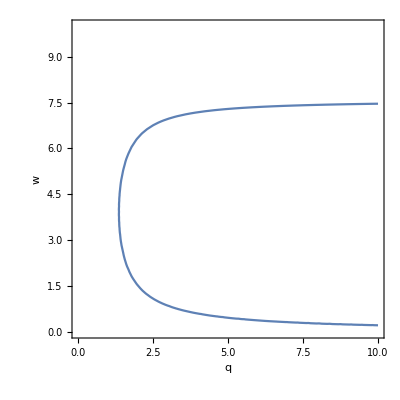

```mathematica
ContourPlot[A[q,w]==1/2,{q,0,10}, {w,0,10},AxesLabel->Automatic]
```

```mathematica
FindMinimum[{q,A[q,w]==1/2},{q,w}]
```

{1.36183,{q→1.36183,w→3.92155}}

```mathematica
A[1.36,4]
```

0.499872

```mathematica
Aq[q_,w_]=Simplify[D[A[q,w], q]]
```

-((4 w^2 (-1+q^2 w)-4 w (-1+2 q w+q^2 w (2+w)) Log[1+w]+(-1+(1+6 q+4 q^2) w+q (2+3 q) w^2+q^2 w^3) Log[1+w]^2)/(2 (1+q)^2 w (1+q w)^2 Log[1+w]))

```mathematica
Simplify[Aq[q,w] 2 (1+q)^2 (1+q w)^2]
```

-4+8 q w+4 q^2 w (2+w)-(4 w (-1+q^2 w))/Log[1+w]+(-1+1/w-2 q (3+w)-q^2 (4+3 w+w^2)) Log[1+w]

```mathematica
Plot3D[Aq[q,w],{q,1, 10}, {w, 1, 10},AxesLabel->Automatic,PlotRange->Full]
```

-Graphics3D-

```mathematica
Plot3D[(q + 1)/q A[q,w],{q,1, 10}, {w, 1, 10},AxesLabel->Automatic,PlotRange->Full]
```

-Graphics3D-

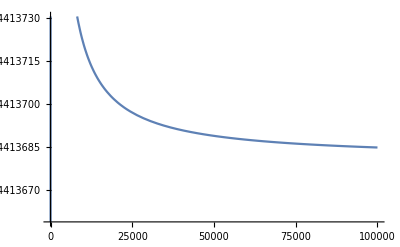

```mathematica
Plot[A[q,10],{q,1,100000}]
```

```mathematica
f[w_]=(4 w-(w+3) Log[w+1])/(2 w)
```

(4 w-(3+w) Log[1+w])/(2 w)

```mathematica
Ainf[w_]=(4 w-(w+3) Log[w+1])/(2 w)
DAinf[w_]=Simplify[D[Ainf[w],w]]
D2Ainf[w_]=Simplify[D[DAinf[w],w]]
```

(4 w-(3+w) Log[1+w])/(2 w)

(-w (3+w)+3 (1+w) Log[1+w])/(2 w^2 (1+w))

((w (6+9 w+w^2))/(1+w)^2-6 Log[1+w])/(2 w^3)

```mathematica
N[Ainf[1]]
```

0.613706

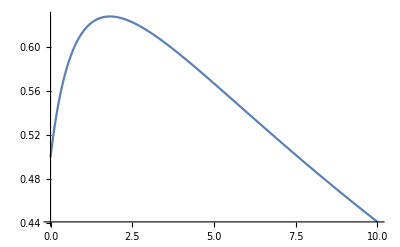

```mathematica
Plot[Ainf[w], {w,0,10}]
```

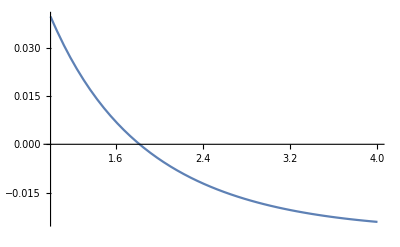

```mathematica
Plot[DAinf[w],{w,1,4}]
```

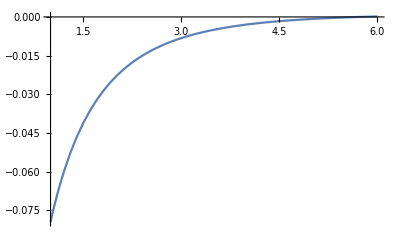

```mathematica
Plot[D2Ainf[w],{w,1,6}]
```

```mathematica
N[D2Ainf[4]]
```

-0.0029424

```mathematica
df[w_]=D[f[w],w]
```

(4-(3+w)/(1+w)-Log[1+w])/(2 w)-(4 w-(3+w) Log[1+w])/(2 w^2)

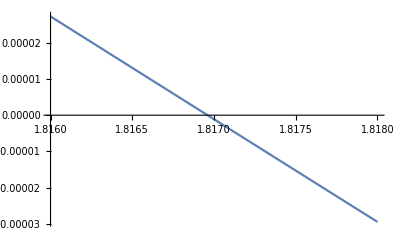

```mathematica
Plot[df[w],{w,1.816,1.818}]
```

```mathematica
f[1.817]
```

0.627178

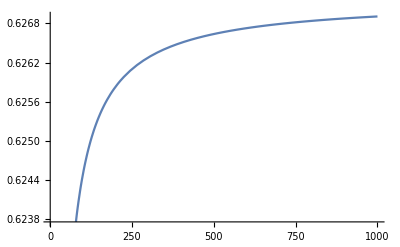

```mathematica
Plot[A[q,1.817],{q,1,1000}]
```

```mathematica
B[q_,w_]=(-(w-1)/w Log[1+w]+4 w/Log[1+w]-4)/(2 (q w+1))
```

(-4+(4 w)/Log[1+w]+((1-w) Log[1+w])/w)/(2 (1+q w))

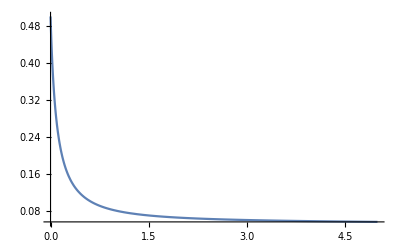

```mathematica
Plot[B[10,w],{w,0,5},PlotRange->Full]
```

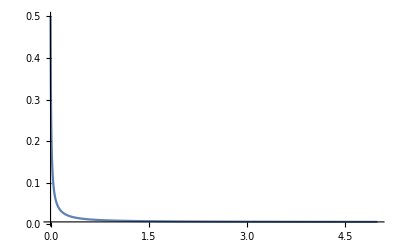

```mathematica
Plot[B[100,w],{w,0,5},PlotRange->Full]
```

```mathematica
Ai[r_,w_]=Simplify[A[1/r,w]]
```

(4 r w^2+4 w (-r+w) Log[1+w]-(r (-1+w)+w (3+w)) Log[1+w]^2)/(2 (1+r) w (r+w) Log[1+w])

```mathematica
N[Ai[1,1]]
```

0.374774

```mathematica
ser=Series[Ai[r,w],{r,0,2}]
```

(2-1/2 Log[1+w]-(3 Log[1+w])/(2 w))+(-2-4/w+2/Log[1+w]+1/2 Log[1+w]+(2 Log[1+w])/w^2+(3 Log[1+w])/(2 w)) r+(2+4/w^2+4/w-2/Log[1+w]-2/(w Log[1+w])-1/2 Log[1+w]-(2 Log[1+w])/w^3-(2 Log[1+w])/w^2-(3 Log[1+w])/(2 w)) r^2+O[r]^3

```mathematica
Ai1[r_,w_]=Simplify[A[1/r,w] (r+1)]
```

(4 r w^2+4 w (-r+w) Log[1+w]-(r (-1+w)+w (3+w)) Log[1+w]^2)/(2 w (r+w) Log[1+w])

```mathematica
Plot3D[Ai[r,w],{r,0,1},{w,0,10}]
```

-Graphics3D-

```mathematica
Plot3D[Ai[r,w],{r,0,1},{w,0,2}]
```

-Graphics3D-

```mathematica
Simplify[D[Ai1[r,w],r] 2 (w+r)^2]
```

(4 (w-Log[1+w])^2)/Log[1+w]

```mathematica
DAi[r_,w_]=Simplify[D[Ai[r,w],r]]
DAi1[r_,w_]=Simplify[D[Ai1[r,w],r]]
```

(4 w^2 (-r^2+w)-4 w (-r^2+2 r w+w (2+w)) Log[1+w]+(r^2 (-1+w)+2 r w (3+w)+w (4+3 w+w^2)) Log[1+w]^2)/(2 (1+r)^2 w (r+w)^2 Log[1+w])

(2 (w-Log[1+w])^2)/((r+w)^2 Log[1+w])

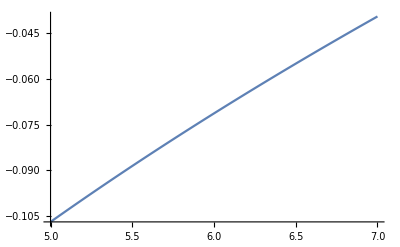

```mathematica
Plot[DAi[0,w],{w,5,7}]
```

```mathematica
Series[DAi[r,w] (2 (1+r)^2 w (r+w)^2), {r,0,3}]
```

(-8 w^2-4 w^3+(4 w^3)/Log[1+w]+4 w Log[1+w]+3 w^2 Log[1+w]+w^3 Log[1+w])+(-8 w^2+6 w Log[1+w]+2 w^2 Log[1+w]) r+(4 w-(4 w^2)/Log[1+w]-Log[1+w]+w Log[1+w]) r^2+O[r]^4

```mathematica
g[r_,w_]=4 w^2/(w+r)^2 (1/Log[1+w])-w/r^2
Simplify[D[g[r,w],w]]
Plot3D[g[r,w],{w,0,1000},{r,0,1}]
Plot3D[DAi1[r,w],{w,0,10},{r,0,1}]
```

-w/r^2+(4 w^2)/((r+w)^2 Log[1+w])

-1/r^2-(4 w^2)/((1+w) (r+w)^2 Log[1+w]^2)+(8 r w)/((r+w)^3 Log[1+w])

-Graphics3D-

-Graphics3D-

```mathematica
N[g[1,0.1]]
```

0.246845

```mathematica
Plot3D[DAi[r,w],{r,0,1},{w,0,10},PlotRange->Full]
```

-Graphics3D-

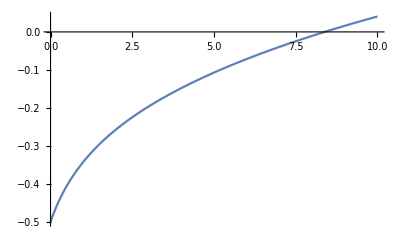

```mathematica
Plot[(-4 w^2-8 w+4 w^2/Log[1+w]+(w^2+3 w+4) Log[1+w])/(2 w^2),{w,0,10}]
```

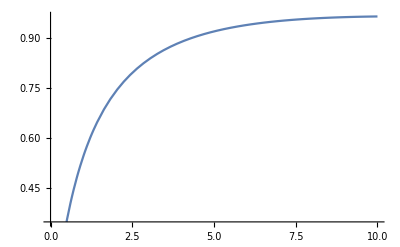

```mathematica
Plot[4/(w^2 Log[1+w])(w-Log[1+w])^2,{w,0,10}]
```

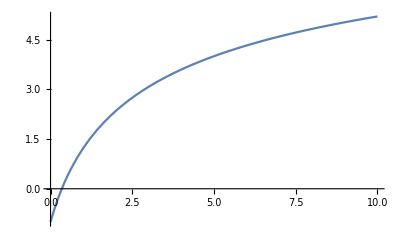

```mathematica
Plot[(w-1)/w Log[1+w]-4 Log[1+w]/w+4,{w,0,10}]
```

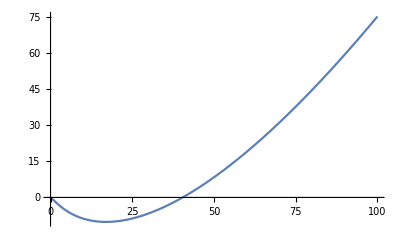

```mathematica
Plot[(w+3) Log[1+w]-4 w,{w,0,100}]
```

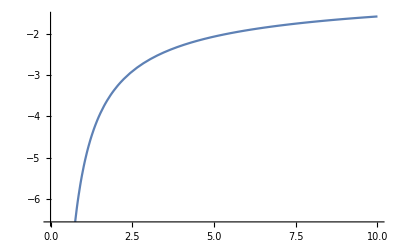

```mathematica
Plot[-4/Log[1+w]+1/(w+1),{w,0,10}]
```

```mathematica
Series[Ai1[r,w],{r,0,2}]
```

(2-1/2 Log[1+w]-(3 Log[1+w])/(2 w))+(-4/w+2/Log[1+w]+(2 Log[1+w])/w^2) r+(4/w^2-2/(w Log[1+w])-(2 Log[1+w])/w^3) r^2+O[r]^3

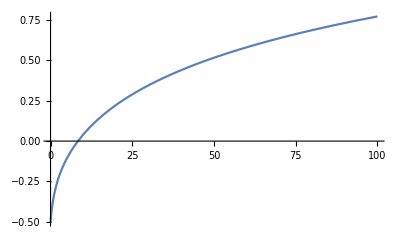

```mathematica
Plot[1/(2 w^2 Log[1+w])(4 w^2-8 w Log[1+w]-4 w^2 Log[1+w]+4 Log[1+w]^2+3 w Log[1+w]^2+w^2 Log[1+w]^2),{w,0,100}]
```

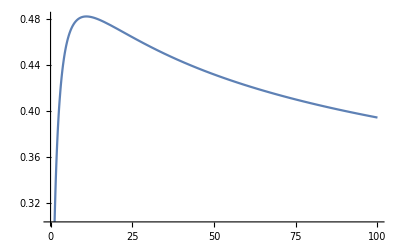

```mathematica
Plot[(-4/w+2/Log[1+w]+(2 Log[1+w])/w^2),{w,0,100}]
```

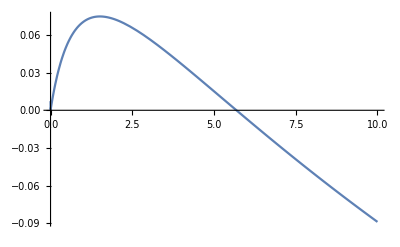

```mathematica
Plot[1/(2 w^3 Log[1+w])(-4 w^2-4 w^3+8 w Log[1+w]+8 w^2 Log[1+w]+4 w^3 Log[1+w]-4 Log[1+w]^2-4 w Log[1+w]^2-3 w^2 Log[1+w]^2-w^3 Log[1+w]^2),{w,0,10}]
```

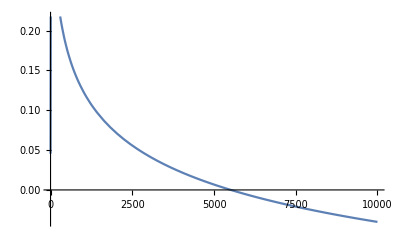

```mathematica
Plot[A[0.1,w],{w,0,10000}]
```

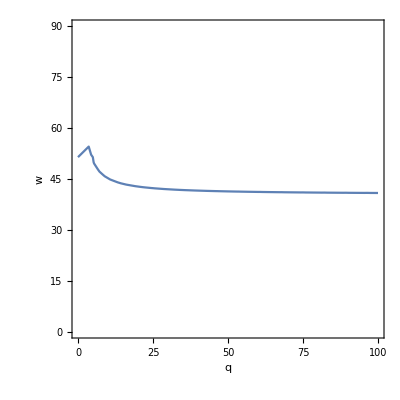

```mathematica
ContourPlot[A[q,w]==0,{q,0,100}, {w,0,90},AxesLabel->Automatic]
```

```mathematica
Series[A[q,w],{q,0,2}]
```

(-2+(2 w)/Log[1+w]-1/2 Log[1+w]+Log[1+w]/(2 w)) q+(2+4 w-(2 w)/Log[1+w]-(2 w^2)/Log[1+w]-3/2 Log[1+w]-Log[1+w]/(2 w)) q^2+O[q]^3

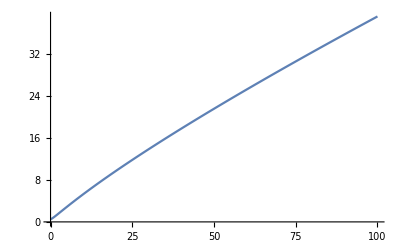

```mathematica
Plot[(-2+(2 w)/Log[1+w]-1/2 Log[1+w]+Log[1+w]/(2 w)),{w,0,100}]
```

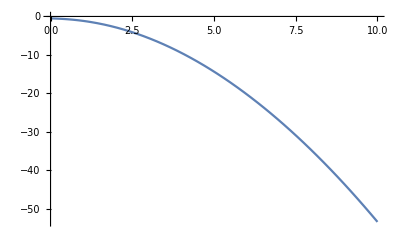

```mathematica
Plot[(2+4 w-(2 w)/Log[1+w]-(2 w^2)/Log[1+w]-3/2 Log[1+w]-Log[1+w]/(2 w)),{w,0,10}]
```

```mathematica
FindMaximum[{A[q,w],q≤1},{q,w}]
```

{0.474998,{q→0.999999,w→4.70952}}

```mathematica
FindMaximum[{A[q,w] (q+1)/q,q≤1,q≥0},{q,w}]
```

{456641.,{q→0.,w→3.43628×10^6}}

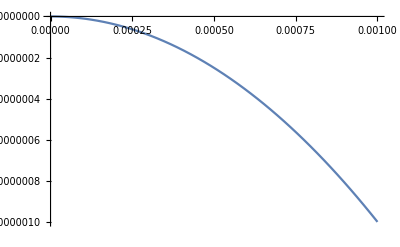

```mathematica
Plot[-4 w^2+4 w^2/Log[1+w]+w^2 Log[1+w]+3 w Log[1+w]-8 w+4 Log[1+w],{w,0,0.001}]
```